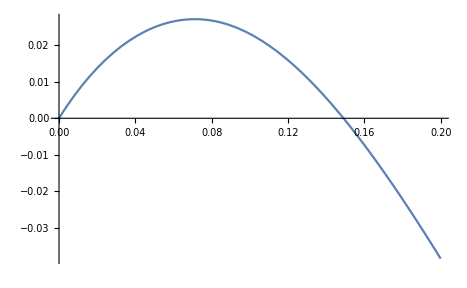

-Graphics-

```mathematica
param= {v0-> 1, α0 ->1, m->0.1, k->1, g -> 9.8};

sol1 = NDSolve[{m ξ''[t] + k (ξ'[t])^2 == 0, ξ[0] == 0, ξ'[0] == v0 Cos[α0]} /. param, ξ[t], {t, 0, 1}];
sol2 = NDSolve[{m y''[t] + k(y'[t])^2 Sign[y'[t]] + m g== 0, y[0] == 0, y'[0] == v0 Sin[α0]} /. param, y[t], {t, 0, 1}];
Plot[y[t]/.sol2,{t, 0 , 0.2}]
ParametricPlot[{ξ[t]/. sol1, y[t] /. sol2},{t, 0 , 0.2}]
```